```mathematica
(*(C) Copyright Jasper Kranias,2023.
This code is licensed under the Apache License,Version 2.0.You may
obtain a copy of this license in the LICENSE.txt file in the root directory
of this source tree or at http://www.apache.org/licenses/LICENSE-2.0.#
Any modifications or derivative works of this code must retain this
copyright notice,and modified files need to carry a notice indicating
that they have been altered from the originals.
*)

(*to find the gaussian state after the oporations of the interferometer setup we use the formalism in "Gaussian states and operations – a quick reference" by Jonatan Bohr Brask (https://arxiv.org/pdf/2102.05748.pdf) *)
(*v is r^bar, s is covariance matrix, a1 is Re(alpha), a2 is Im(alpha), etc*)
(*t is used in place of theta*)


(*identity matrix of dimension n by n*)
id[n_]:=id[n]=IdentityMatrix[n]

(*Permutation matrix of desired permutation in n dim*)
(*perm is a list of numbers, and the output P[perm] is a matrix which permutes the entires of a vector to that order*)
(* ex. perm={3,2,1,4}, P[perm].{a,b,c,d}={c,b,a,d} *)
P[perm_]:=Permute[id[Length[perm]],PermutationCycles[perm]]ᵀ


(*we start with an initial v and s written below*)

a1=.
a2=.
b1=.
b2=.
c1=.
c2=.

(*initial means vector with coherent seeding in a and b*)
v0=Sqrt[2]{a1,a2,b1,b2,c1,c2};

(*initial covariance matrix*)
s0=(1/2)*id[6];


(*the following lists are permuataions pmn which are used when modes m and n are transformed (or pm if a single mode m is transformed)*)

(*for operations which affect one mode*)
pa={1,2,3,4,5,6};
pb={3,4,1,2,5,6};
pc={5,6,1,2,3,4};

(*for operations which affect two modes*)
pab={1,2,3,4,5,6};
pac={1,2,5,6,3,4};
pbc={3,4,5,6,1,2};

(*for loss, which affects one mode and a ficticious mode*)
paf={1,2,7,8,3,4,5,6};
pbf={3,4,7,8,1,2,5,6};
pcf={5,6,7,8,1,2,3,4};


(*the following sections for each Gaussian operation OP define the matrix FOP which transforms s as F.s.Fᵀ and v as F.v*)

(*each operation starts with a smaller matrix f which affects one or two modes, then f is used along with an identity matrix to form a block matrix F in the space of all modes, then the block matrix is multiplied by permuation matrices as P^(-1).F.P so it acts on the correct modes*)

(*each section also defines the functions OPs and OPv which output the resulting s and v from the operation*)


(*TWO MODE SQUEEZING (TMS)*)

(*S_theta matrix used in fTMS*)
(*input the squeezing phase t*)
St[t_]:={{Cos[t],Sin[t]},{Sin[t],-Cos[t]}}

(*f for TMS*)
(*input the squeezing magnitude r and phase t*)
fTMS[r_,t_]:=ArrayFlatten[{{Cosh[r]*id[2],-Sinh[r]*St[t]},{-Sinh[r]*St[t],Cosh[r]*id[2]}}]

(*F for TMS*)
(*input either s or v (it is only to get the correct dimension), permuation order, squeezing magnitude r, phase t*)
FTMS[s_,ord_,r_,t_]:=Inverse[P[ord]].ArrayFlatten[{{fTMS[r,t],0},{0,id[Length[s]-4]}}].P[ord]


(*performs two mode squeezing transformation of s and v on desired modes with squeeze parameter re^(it)*)
(*performed on the first two modes of ord*)
TMSs[s_,ord_,r_,t_]:=FTMS[s,ord,r,t].s.FTMS[s,ord,r,t]ᵀ
TMSv[v_,ord_,r_,t_]:=FTMS[v,ord,r,t].v



(*BEAM SPLITTER (BS)*)

(*f for BS*)
(*input transmittivity T*)
fBS[T_]:=ArrayFlatten[{{Sqrt[T]*id[2],Sqrt[1-T]*id[2]},{-Sqrt[1-T]*id[2],Sqrt[T]*id[2]}}]


(*F for BS*)
(*input order and trasnmitivity T*)
FBS[s_,ord_,T_]:=Inverse[P[ord]].ArrayFlatten[{{fBS[T],0},{0,id[Length[s]-4]}}].P[ord]


(*functions that perform regular beam splitting with transmittivity T in the first mode of the ordering ord*)
(*performed on the first two modes of ord*)
BSs[s_,ord_,T_]:=FBS[s,ord,T].s.FBS[s,ord,T]ᵀ
BSv[v_,ord_,T_]:=FBS[v,ord,T].v



(*LOSS (L)*)

(*F for ficticious beam spliiter*)
(*input order and trasnmitivity T*)
FL[s_,ord_,T_]:=Inverse[P[ord]].ArrayFlatten[{{fBS[T],0},{0,id[Length[s]-2]}}].P[ord]
(*!!! potentail typo with earlier results, this used to be just BS not fBS*)

(*functions that perform loss by adding in a ficticious mode, putting it through a ficticious beam splitter with the lossy mode, and then cutting out the ficticious mode*)
(*use ord=pmf for loss in mode m*)
Ls[s_,ord_,T_]:=(sint=ArrayFlatten[{{s,0},{0,(1/2)*id[2]}}]; sint2=FL[s,ord,T].sint.FL[s,ord,T]ᵀ; sint2[[1;;Length[s],1;;Length[s]]])
Lv[v_,ord_,T_]:=(vint=Append[v,0];vint2=Append[vint,0]; vint3=FL[v,ord,T].vint2; vint3[[1;;Length[v]]])



(*PHASE SHIFT (P)*)

(*f for P*)
(*input phase shift phi*)
fP[phi_]:={{Cos[phi],Sin[phi]},{-Sin[phi],Cos[phi]}}

(*F for P*)
(*input phase shift phi*)
FP[s_,ord_,phi_]:=Inverse[P[ord]].ArrayFlatten[{{fP[phi],0},{0,id[Length[s]-2]}}].P[ord]

(*functions that perform phase shifting by phi in the first mode of ord*)
Ps[s_,ord_,phi_]:=FP[s,ord,phi].s.FP[s,ord,phi]ᵀ
Pv[v_,ord_,phi_]:=FP[v,ord,phi].v


(*new functions could be defined to perform other operations, so long as they are Gaussian*)



(*now we move on to functions which compute the QFI from the Gaussian state*)
(*this follows the formalism by Safranek: https://iopscience.iop.org/article/10.1088/1751-8121/aaf068/pdf. We use equation A11, the real form of the QFI for mixed states*)


(*vectorizes a matrix m*)
Vec[m_]:=ArrayReshape[Transpose[m],{Times@@Dimensions[m],1}]

(*finds M given s*)
(*old omega version Omg=KroneckerProduct[id[(Length[s]/2)],{{0,1},{-1,0}}]*)
M[s_]:=(Omg=ArrayFlatten[{{0,id[Length[s]/2]},{-id[Length[s]/2],0}}];FullSimplify[KroneckerProduct[s,s]-KroneckerProduct[Omg,Omg]])

(*finds QFI for given s, v, and phi*)
(*this version solves M.Vec[D[s,phi] to find Inverse[M].Vec[D[s,phi], this works fine numerically but not when doing things analytically*)
(*maybe this is faster than the other method numerically, could be worth investigating*)
FISalt[s_,v_,phival_]:=(ds=Vec[D[s,phi]];dv=D[v,phi];phi=phival;(1/2)*dsᵀ.LinearSolve[M[s],ds]+2*dv.Inverse[s].dv)


(*constructs the diagonal matrix of eigenvalues to be used in FIS*)
Lam[evals_]:=(lam={};Do[lam=Append[lam,evals[[i]]*UnitVector[Length[evals],i]],{i,Length[evals]}];lam)


(*finds QFI using alternate form of M inverse shown in section 9 of the overleaf, can keep phi as a variable*)
FIS[s_,v_,phival_]:=(ds=Simplify[Vec[D[s,phi]]];dv=D[v,phi];
sinv=Simplify[Inverse[s]];
phi=phival;Omg=ArrayFlatten[{{0,id[Length[s]/2]},{-id[Length[s]/2],0}}];{evals,evecs}=Eigensystem[Simplify[(s.Omg)]];q=Simplify[Transpose[evecs]];
l=Simplify[Lam[evals]];Linv=Simplify[Inverse[id[(Length[s])^2]-KroneckerProduct[l,l]]];qinv=Simplify[Inverse[q]];
Ainv=Simplify[KroneckerProduct[sinv,sinv]];
Q=Simplify[KroneckerProduct[q,q]];
Qinv=Simplify[KroneckerProduct[qinv,qinv]];
Minv=Simplify[Ainv-Ainv.Q.Linv.Qinv];
Simplify[((1/2)*dsᵀ.Minv.ds+2*dv.sinv.dv)[[1,1]]])


(*finds QFI for pure state*)
FISpure[s_,v_,phival_]:=(ds=D[s,phi];dv=D[v,phi];phi=phival;
sinv=Simplify[Inverse[s]];
Simplify[(1/4)*Tr[sinv.ds.sinv.ds]+2dv.sinv.dv])

(*only first term*)
sIQ[s_,v_,phival_]:=(ds=Simplify[Vec[D[s,phi]]];
sinv=Simplify[Inverse[s]];
phi=phival;Omg=ArrayFlatten[{{0,id[Length[s]/2]},{-id[Length[s]/2],0}}];{evals,evecs}=Eigensystem[Simplify[(s.Omg)]];q=Simplify[Transpose[evecs]];
l=Simplify[Lam[evals]];Linv=Simplify[Inverse[id[(Length[s])^2]-KroneckerProduct[l,l]]];qinv=Simplify[Inverse[q]];
Ainv=Simplify[KroneckerProduct[sinv,sinv]];
Q=Simplify[KroneckerProduct[q,q]];
Qinv=Simplify[KroneckerProduct[qinv,qinv]];
Minv=Simplify[Ainv-Ainv.Q.Linv.Qinv];
Simplify[((1/2)*dsᵀ.Minv.ds)[[1,1]]])

(*only second term*)
dIQ[s_,v_,p_]:=(phi=.; dv=D[v,phi];phi=p; sinv=FullSimplify[Inverse[s]]; Simplify[2*dv.sinv.dv])



(*here we define functions that take in an initaial s and v, then output the s and v after certain Gaussian transformations*)
(*to account for the differences between the Brask and Safrenek formalisms, the basis of s and v must be reordered from the quadratures x1,p1,x2,p2,... to x1,x2,...,p1,p2,... and s must be multipled by 2*)


(*No external loss*)
YMI[s_,v_,r1_,t1_,T_]:=(phi=.;
s1=TMSs[s,pab,r1,t1]; v1=TMSv[v,pab,r1,t1]; 
s2=Ls[s1,paf,T];v2=Lv[v1,paf,T];
s3=Ls[s2,pbf,T];v3=Lv[v2,pbf,T]; 
s4=Ps[s3,pa,phi];v4=Pv[v3,pa,phi];
s8=s4[[1;;4,1;;4]];v8=v4[[1;;4]];  
Pord=P[{1,3,2,4}]; 
s9=2*Pord.s8.Pordᵀ; v9=Pord.v8; 
{FullSimplify[s9],FullSimplify[v9]})

(*Yurke with both types of loss*)
Yurke[s_,v_,r1_,t1_,r2_,t2_,T_,n_]:=(phi=.;
s1=TMSs[s,pab,r1,t1]; v1=TMSv[v,pab,r1,t1]; 
s2=Ls[s1,paf,T];v2=Lv[v1,paf,T];
s3=Ls[s2,pbf,T];v3=Lv[v2,pbf,T]; 
s4=Ps[s3,pa,phi];v4=Pv[v3,pa,phi];
s5=TMSs[s4,pab,r2,t2]; v5=TMSv[v4,pab,r2,t2]; 
s6=Ls[s5,paf,n];v6=Lv[v5,paf,n];
s7=Ls[s6,pbf,n];v7=Lv[v6,pbf,n];
s8=s7[[1;;4,1;;4]];v8=v7[[1;;4]];  
Pord=P[{1,3,2,4}]; 
s9=2*Pord.s8.Pordᵀ; v9=Pord.v8; 
{FullSimplify[s9],FullSimplify[v9]})




(*Mandel with both internal and external loss*)
Mandel[s_,v_,r1_,t1_,r2_,t2_,T_,n_]:=(phi=.;
s1=TMSs[s,pab,r1,t1]; v1=TMSv[v,pab,r1,t1];
s2=Ls[s1,paf,T]; v2=Lv[v1,paf,T]; 
s3=Ls[s2,pbf,T]; v3=Lv[v2,pbf,T]; 
s4=Ps[s3,pa,phi];v4=Pv[v3,pa,phi]; 
s5=TMSs[s4,pac,r2,t2]; v5=TMSv[v4,pac,r2,t2];s6=Ls[s5,paf,n]; v6=Lv[v5,paf,n];
s8=BSs[s6,pbc,1/2]; v8=BSv[v6,pbc,1/2];
s9=Ls[s8,pbf,n]; v9=Lv[v8,pbf,n];
s10=Ls[s9,pcf,n];v10=Lv[v9,pcf,n];
Pord=P[{1,3,5,2,4,6}];
s11=2*Pord.s10.Pordᵀ;v11=Pord.v10;
{FullSimplify[s11],FullSimplify[v11]})


(*Mandel with mode a cut out at the end*)
Mandelnoa[s_,v_,r1_,t1_,r2_,t2_,T_,n_]:=(phi=.;
s1=TMSs[s,pab,r1,t1]; v1=TMSv[v,pab,r1,t1];
s2=Ls[s1,paf,T]; v2=Lv[v1,paf,T]; 
s3=Ls[s2,pbf,T]; v3=Lv[v2,pbf,T]; 
s4=Ps[s3,pa,phi];v4=Pv[v3,pa,phi]; 
s5=TMSs[s4,pac,r2,t2]; v5=TMSv[v4,pac,r2,t2];s6=Ls[s5,paf,n]; v6=Lv[v5,paf,n];
s8=BSs[s6,pbc,1/2]; v8=BSv[v6,pbc,1/2];
s9=Ls[s8,pbf,n]; v9=Lv[v8,pbf,n];
s10=Ls[s9,pcf,n];v10=Lv[v9,pcf,n];
s11=s10[[3;;6,3;;6]]; v11=v10[[3;;6]];
Pord=P[{1,3,2,4}];
s12=2*Pord.s11.Pordᵀ;v12=Pord.v11;
{FullSimplify[s12],FullSimplify[v12]})


(*MZI*)
MZI[s_,v_,T_,n_]:=(phi=.;
s1=BSs[s,pab,1/2]; v1=BSv[v,pab,1/2];
s2=Ls[s1,paf,T]; v2=Lv[v1,paf,T];
s3=Ls[s2,pbf,T]; v3=Lv[v2,pbf,T];
s4=Ps[s3,pa,phi];v4=Pv[v3,pa,phi];
s5=BSs[s4,pab,1/2]; v5=BSv[v4,pab,1/2];
s6=Ls[s5,paf,n]; v6=Lv[v5,paf,n];
s7=Ls[s6,pbf,n]; v7=Lv[v6,pbf,n];
s8=s7[[1;;4,1;;4]];v8=v7[[1;;4]];  
Pord=P[{1,3,2,4}]; 
s9=2*Pord.s8.Pordᵀ; v9=Pord.v8; 
{FullSimplify[s9],FullSimplify[v9]})



(*caluclates QFI for a given transformation and phase shift p*)
(*input the transformation function with its parameters, or equivalently, input a list {s,v} describing the final state*)
QFI[state_,p_]:=(phi=.;Simplify[FIS[state[[1]],state[[2]],p]])

(*calculates just the second term in QFI equation given the transformation and phi*)
dIQ[state_,p_]:=(phi=.; dv=D[state[[2]],phi]; sinv=Simplify[Inverse[state[[1]]]];
phi=p; Simplify[2*dv.sinv.dv])

(*Unitary to convert real form to complex form*)
U[s_]:=(num=Length[s]/2;
(1/Sqrt[2])*ArrayFlatten[{{id[num],ⅈ*id[num]},{id[num],-ⅈ*id[num]}}])

(*symplectic K for complex form*)
Kmat[s]:=(num=Length[s]/2;ArrayFlatten[{{id[num],0},{0,-id[num]}}])

(*A=Ks matrix from https://iopscience.iop.org/article/10.1088/1367-2630/17/7/073016/pdf*)
(*first have to convert to complex form*)
Amat[s_]:=(len=Length[s]/2;sig=U[s].s.ConjugateTranspose[U[s]]; 
FullSimplify[K[len].sig])

(*expression for first term of two-mode QFI from https://iopscience.iop.org/article/10.1088/1367-2630/17/7/073016/pdf*)
(*only gives first term, must add on dIQ term for full expression*)

HIQ[s_]:=(num2=Length[s];
A=FullSimplify[Amat[s]];
detA=FullSimplify[Det[A]];
A2=FullSimplify[MatrixPower[A,2]];
dA=FullSimplify[D[A,phi]];
trA2=FullSimplify[Tr[A2]];
invA=FullSimplify[Inverse[A]];
root=FullSimplify[Sqrt[trA2^2-16*detA]];
lam1=FullSimplify[(1/2)*Sqrt[trA2+root]];
lam2=FullSimplify[(1/2)*Sqrt[trA2-root]];
dlam1=FullSimplify[D[lam1,phi]];
dlam2=FullSimplify[D[lam2,phi]];
FullSimplify[(1/(2*(detA-1)))*( detA*Tr[MatrixPower[invA.dA,2]]+Sqrt[Det[id[num2]+A2]]*Tr[MatrixPower[Inverse[id[num2]+A2].dA,2]]+4*(lam1^2-lam2^2)*(-(dlam1^2)/(lam1^4-1)+(dlam2^2)/(lam2^4-1)))]
)

(*IQ from complex formalism*)
(*must have s,v as complex already*)
CIQ[s_,v_]:=(K=Kmat[s];
ds=FullSimplify[D[s,phi]];
dv=FullSimplify[D[v,phi]];
A=FullSimplify[s.K];
{evals,evecs}=Eigensystem[A];
l=Lam[FullSimplify[evals]];
q=Transpose[FullSimplify[evecs]];
qinv=FullSimplify[Inverse[q]];
Sig=FullSimplify[qinv.ds.K.q];
Dinv=FullSimplify[Inverse[KroneckerProduct[l,l]-id[(Length[s])^2]]];
Kt=ArrayFlatten[{{0,-id[Length[s]/2]},{id[Length[s]/2],0}}];
FullSimplify[(1/2)*Transpose[Vec[Transpose[Sig]]].Dinv.Vec[Sig]+2*dv.Kt.q.Inverse[l].qinv.dv]
)
```

```mathematica
T=.;
n=.;
r1=.;
r2=.;
t1=.;
t2=.;


psi=Mandel[s0,v0,r1,t1,r2,t2,1,n];
sr=psi[[1]];
s=FullSimplify[U[sr].sr.ConjugateTranspose[U[sr]]];
K=Kmat[s];
B=FullSimplify[s.K];
```

```mathematica
FullSimplify[Eigenvalues[B]]
```

{-1,1,-ⅈ √(-1-3 (-1+n) n+(-1+n) n (2 Cosh[2 r1] Cosh[r2]^2+Cosh[2 r2])),-ⅈ √(-1-3 (-1+n) n+(-1+n) n (2 Cosh[2 r1] Cosh[r2]^2+Cosh[2 r2])),ⅈ √(-1-3 (-1+n) n+(-1+n) n (2 Cosh[2 r1] Cosh[r2]^2+Cosh[2 r2])),ⅈ √(-1-3 (-1+n) n+(-1+n) n (2 Cosh[2 r1] Cosh[r2]^2+Cosh[2 r2]))}

```mathematica
(*note that Cosh[2r1]+2Cosh[r1]^2Cosh[2r2]-3=4(Cosh[r1]^2Cosh[r2]^2-1), so we can simplify the eigenvalues:*)
evals={-1,1,-Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],-Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)]}
```

{-1,1,-√(1+4 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2)),-√(1+4 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2)),√(1+4 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2)),√(1+4 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2))}

```mathematica
vec={w1,w2,w3,w4,w5,w6};

(*finding eigenspace for each eigenvalue
skipped 4 and 6 due to degeneracy
using solve since Nullspace[] sometimes gives no eignenvectors, or only one when there should be two
*)

zero1=(B-evals[[1]]*id[6]).vec;
FullSimplify[Solve[zero1=={0,0,0,0,0,0},vec]]

zero2=(B-evals[[2]]*id[6]).vec;
FullSimplify[Solve[zero2=={0,0,0,0,0,0},vec]]

zero3=(B-evals[[3]]*id[6]).vec;
FullSimplify[Solve[zero3=={0,0,0,0,0,0},vec]]

zero5=(B-evals[[5]]*id[6]).vec;
FullSimplify[Solve[zero5=={0,0,0,0,0,0},vec]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w1→0,w2→0,w3→0,w4→0,w6→w5 (-1+1/(1/2-1/2 ⅇ^(ⅈ (phi-t1+t2)) Coth[r1] Sinh[r2]))}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w1→0,w3→(w2 (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]-ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]),w4→0,w5→0,w6→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w1→-((ⅇ^(ⅈ (t1+t2)) w5 (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),w3→w2-(2 ⅇ^(ⅈ t1) w2 Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),w4→-((ⅇ^(ⅈ phi) w2 (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),w6→w5-(2 ⅇ^(ⅈ (phi+t2)) w5 Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w1→-((ⅇ^(ⅈ (t1+t2)) w5 (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),w3→w2-(2 ⅇ^(ⅈ t1) w2 Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),w4→-((ⅇ^(ⅈ phi) w2 (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),w6→w5-(2 ⅇ^(ⅈ (phi+t2)) w5 Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])}}

```mathematica
(*now constuct matrix of eigenvectors*)
(*for the 3rd eval w2 and w5 are independent so we get one vector by choosing w2=1,w5=0, and another by choosing w2=0, w5=1 (and similar for the 5th eval)*)
q=Transpose[{{0,0,0,0,1,-1+1/(1/2-1/2 ⅇ^(ⅈ (phi-t1+t2)) Coth[r1] Sinh[r2])},{0,1,(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]-ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]),0,0,0},{0,1,1-(2 ⅇ^(ⅈ t1)Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),-((ⅇ^(ⅈ phi) (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),0,0},{-((ⅇ^(ⅈ (t1+t2)) (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),0,0,0,1,1-(2 ⅇ^(ⅈ (phi+t2))Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])},{0,1,1-(2 ⅇ^(ⅈ t1)Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),-((ⅇ^(ⅈ phi)(1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),0,0},{-((ⅇ^(ⅈ (t1+t2))(1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),0,0,0,1,1-(2 ⅇ^(ⅈ (phi+t2))Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])}}];
l=Lam[evals];
```

```mathematica
(*now verify that the eigendecomposition is correct*)
qinv=FullSimplify[Inverse[q]];
decomp=FullSimplify[q.l.qinv];
```

```mathematica
MatrixForm[B]
MatrixForm[decomp]
```

(1/2 (2-3 n+n Cosh[2 r1]+2 n Cosh[r1]^2 Cosh[2 r2]) | 0 | 0 | 0 | (ⅇ^(-ⅈ phi) n Cosh[r2] (ⅇ^(ⅈ t1) Sinh[2 r1]+2 ⅇ^(ⅈ (phi+t2)) Cosh[r1]^2 Sinh[r2]))/(√2) | -(n Cosh[r2] (ⅇ^(-ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2)
0 | 1/4 (4-3 n+n (1+2 Cosh[2 r1]) Cosh[r2]^2+n Sinh[r2] (4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2])) | 1/4 n (1-3 Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]-4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2]) | (ⅇ^(-ⅈ phi) n Cosh[r2] (ⅇ^(ⅈ t1) Sinh[2 r1]+2 ⅇ^(ⅈ (phi+t2)) Cosh[r1]^2 Sinh[r2]))/(√2) | 0 | 0
0 | 1/4 n (1-3 Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]+4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2]) | 1/4 (4-3 n+n (1+2 Cosh[2 r1]) Cosh[r2]^2+n Sinh[r2] (-4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2])) | -(n Cosh[r2] (ⅇ^(-ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2) | 0 | 0
0 | (n Cosh[r2] (-ⅇ^(ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(-ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2) | (n Cosh[r2] (ⅇ^(ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(-ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2) | 1/2 (-2+3 n-n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2])) | 0 | 0
(n Cosh[r2] (-ⅇ^(ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(-ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2) | 0 | 0 | 0 | 1/4 (-4+3 n-n ((1+2 Cosh[2 r1]) Cosh[r2]^2+Sinh[r2] (4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2]))) | -1/4 n (1-3 Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]+4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2])
(n Cosh[r2] (ⅇ^(ⅈ (phi-t1)) Sinh[2 r1]-2 ⅇ^(-ⅈ t2) Cosh[r1]^2 Sinh[r2]))/(√2) | 0 | 0 | 0 | 1/4 n (-1+3 Cosh[2 r1]-2 Cosh[r1]^2 Cosh[2 r2]+4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2]) | 1/4 (-4+3 n-n ((1+2 Cosh[2 r1]) Cosh[r2]^2+Sinh[r2] (-4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2]))))

(1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2 | 0 | 0 | 0 | √2 ⅇ^(-ⅈ phi) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]) | √2 ⅇ^(-ⅈ phi) n Cosh[r1] Cosh[r2] (-ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2])
0 | 1/4 (4-3 n+n (1+2 Cosh[2 r1]) Cosh[r2]^2+n Sinh[r2] (4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2])) | 1/4 n (1+Cosh[r1]^2 (-3+2 Cosh[2 r2])-3 Sinh[r1]^2-4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2]) | √2 ⅇ^(-ⅈ phi) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]) | 0 | 0
0 | n (-Sinh[r1]^2+Sinh[r2] (ⅈ Sin[phi-t1+t2] Sinh[2 r1]+Cosh[r1]^2 Sinh[r2])) | 1/4 (4-3 n+n (1+2 Cosh[2 r1]) Cosh[r2]^2+n Sinh[r2] (-4 Cos[phi-t1+t2] Sinh[2 r1]+Sinh[r2])) | √2 ⅇ^(-ⅈ phi) n Cosh[r1] Cosh[r2] (-ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]) | 0 | 0
0 | -√2 ⅇ^(-ⅈ (t1+t2)) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]) | √2 ⅇ^(-ⅈ (t1+t2)) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ (phi+t2)) Sinh[r1]-ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]) | -1+2 n-2 n Cosh[r1]^2 Cosh[r2]^2 | 0 | 0
-√2 ⅇ^(-ⅈ (t1+t2)) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]) | 0 | 0 | 0 | 1/8 (-8+6 n-n (2 Cosh[2 r1]+Cosh[2 (r1-r2)]+2 Cosh[2 r2]+Cosh[2 (r1+r2)]+8 Cos[phi-t1+t2] Sinh[2 r1] Sinh[r2])) | n (Sinh[r1]^2-Sinh[r2] (ⅈ Sin[phi-t1+t2] Sinh[2 r1]+Cosh[r1]^2 Sinh[r2]))
√2 ⅇ^(-ⅈ (t1+t2)) n Cosh[r1] Cosh[r2] (ⅇ^(ⅈ (phi+t2)) Sinh[r1]-ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]) | 0 | 0 | 0 | 1/4 n (-1+3 Cosh[2 r1]-2 Cosh[r1]^2 Cosh[2 r2]+4 ⅈ Sin[phi-t1+t2] Sinh[2 r1] Sinh[r2]) | 1/4 (-4+3 n-n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]-4 Cos[phi-t1+t2] Sinh[2 r1] Sinh[r2])))

```mathematica
ds=FullSimplify[D[s,phi]];
```

```mathematica
Sig=FullSimplify[qinv.ds.K.q];
```

```mathematica
(*multiplying eigenvalues by a for regularization procedure to avoid singular matrix, will take the limit a->1 at the end*)
Dinv=FullSimplify[Inverse[a*KroneckerProduct[l,l]-id[(Length[s])^2]]];
```

```mathematica
FullSimplify[(1/2)*Transpose[Vec[Transpose[Sig]]].Dinv.Vec[Sig]]
```

```mathematica
boing={{-((2 n^2 (-8 a^2 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(2+a (2+n (-6+4 n+a (-3+(8-7 n) n)))+a (-1+n) (2 (1+a-2 n+a n (-3+4 n)) Cosh[2 r2]+a n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-a^2 (1-2 n)^2+4 a^2 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (1+a+3 a (-1+n) n)+2 a (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))))}}
```

{{-((2 n^2 (-8 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))))}}

```mathematica
a=1
boing[[1,1]]
```

1

-((2 n^2 (-8 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))))

```mathematica
QFIterm1=-((2 n^2 (-8 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))));

(*
first let us consider just the numerator
if we factor out -2n^2Sinh[2r1]^2, we are left with
*)

numerator=-2*n*(1-n)^2*Cosh[r1]^2*Cosh[4*r2]+4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]));
```

```mathematica
FullSimplify[numerator]
```

(-1+n) (-4+(5-7 n) n+2 (2+n (-5+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2])-2 (-1+n) n Cosh[r1]^2 Cosh[4 r2])

```mathematica
(*now use Cosh[r1]^2=C1^2, Cosh[2r1]=2*C1^2-1, Cosh[2r2]=2*C2^2-1, Cosh[4 r2]=Cosh[2r2]^2+Sinh[2r2]^2=8*C2^4-8*C2^2+1
then
-4+(5-7 n) n+2 (2+n (-5+4 n)) Cosh[2 r2]+n*(C1^2+S1^2) (1+n+2 Cosh[2 r2])-2 (-1+n) n Cosh[r1]^2 Cosh[4 r2]=
*)
thing1=-4+(5-7*n)*n+2*(2+n*(-5+4*n))*(2*C2^2-1)+n*(2*C1^2-1)*(1+n+2*(2*C2^2-1))-2*(-1+n)*n*C1^2*(8*C2^4-8*C2^2+1);
thing2=FullSimplify[thing1]
```

-8 (1+2 (-1+n) n+2 C1^2 C2^4 (-1+n) n-C2^2 (-1+2 n) (-1+n+C1^2 n))

```mathematica
numsimp[n_,r1_,r2_]:=(-1+n)*(-8)*(1-2*n*(1-n)*(1+Cosh[r1]^2*Cosh[r2]^4)-Cosh[r2]^2*(2*n-1)* (-1+n*(1+Cosh[r1]^2)))
numorig[n_,r1_,r2_]:=-2*n*(1-n)^2*Cosh[r1]^2*Cosh[4*r2]+4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]));
numsimp[0.8,0.2,0.16]
numorig[0.8,0.2,0.16]
```

-0.0954277

-0.0954277

```mathematica
denominator=(1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]));
FullSimplify[denominator]
```

4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2) (-4-6 (-1+n) n+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))

```mathematica
(*now
-4-6 (-1+n) n+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2])
=-4+6n(1-n)-2n(1-n)(4Cosh[r1]^2Cosh[r2]^2-1)
=-4(1-2n(1-n)(1-Cosh[r1]^2Cosh[r2]^2))

therefore the denominator is
*)
16*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1))
```

```mathematica
(*checking algebra*)

densimp[n_,r1_,r2_]:=16*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1))
denorig[n_,r1_,r2_]:=((1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2])))

densimp[0.23,1.4,1.3]
denorig[0.23,1.4,1.3]
```

337.163

337.163

```mathematica
(*and now the 1st term of the QFI should be*)

thing5=-2*n^2*Sinh[2r1]^2*(-1+n)*(-8)*(1-2*n*(1-n)*(1+Cosh[r1]^2*Cosh[r2]^4)-Cosh[r2]^2*(2*n-1)* (-1+n*(1+Cosh[r1]^2)))/(16*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)));

(*simplifying by hand:*)

thing6=n*Sinh[2*r1]^2*(-1+2*n*(1-n)*(1+Cosh[r1]^2*Cosh[r2]^4)+Cosh[r2]^2*(2*n-1)* (-1+n*(1+Cosh[r1]^2)))/(((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)))
```

(n (-1+(-1+2 n) (-1+n (1+Cosh[r1]^2)) Cosh[r2]^2+2 (1-n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2)/((-1+Cosh[r1]^2 Cosh[r2]^2) (1+2 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))

```mathematica
(*comparing numerically to make sure algebra is correct*)


MQFI1[n_,r1_,r2_]:=n*Sinh[2*r1]^2*(-1+2*n*(1-n)*(1+Cosh[r1]^2*Cosh[r2]^4)+Cosh[r2]^2*(2*n-1)* (-1+n*(1+Cosh[r1]^2)))/(((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)))


MQFI0[n_,r1_,r2_]:=-((2 n^2 (-8 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(4+n (-9+4 n+(8-7 n) n)+(-1+n) (2 (2-2 n+n (-3+4 n)) Cosh[2 r2]+n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-(1-2 n)^2+4 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (2+3 (-1+n) n)+2 (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))))

MQFI1[0.8,0.24,1.1]
MQFI0[0.8,0.24,1.1]
```

0.19045

0.19045

```mathematica
(*checking that analytic QFI caluclation lines up with numerical version, must use parameter nu for regularization procedure*)
(*the a we used when performing the analytic calculation was nu^2, and we also need to add in the factor of a on the outside terms that we didnt bother to do, but is necessary when comparing with the numerical version*)
MQFIa[n_,r1_,r2_,a_]:=-a((2 n^2 (-8 a^2 (-1+n)^2 n Cosh[r1]^4 Cosh[4 r2] Sinh[r1]^2+(2+a (2+n (-6+4 n+a (-3+(8-7 n) n)))+a (-1+n) (2 (1+a-2 n+a n (-3+4 n)) Cosh[2 r2]+a n Cosh[2 r1] (1+n+2 Cosh[2 r2]))) Sinh[2 r1]^2))/((1-a^2 (1-2 n)^2+4 a^2 (-1+n) n Cosh[r1]^2 Cosh[r2]^2) (-2 (1+a+3 a (-1+n) n)+2 a (-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))))


psi=Mandel[s0,v0,0.24,0,1.1,0,1,0.8];
nu=1.1;
aa=nu^2;
sr=(nu)*psi[[1]];
vr=psi[[2]];
FIS[sr,vr,0]
MQFIa[0.8,0.24,1.1,aa]
```

(0.186334-2.06671×10^-17 ⅈ)+2.57016 a1^2+2.57016 a2^2-1.21052 a1 b1+0.142536 b1^2+1.21052 a2 b2+0.142536 b2^2

0.186334

```mathematica
(*now compute the second term of the QFI*)
psi=Mandel[s0,v0,r1,t1,r2,t2,1,n];
sr=psi[[1]];
vr=psi[[2]];
s=FullSimplify[U[sr].sr.ConjugateTranspose[U[sr]]];
v=FullSimplify[U[vr].vr];
dv=FullSimplify[D[v,phi]];
Kt=ArrayFlatten[{{0,-id[Length[s]/2]},{id[Length[s]/2],0}}];
q=Transpose[{{0,0,0,0,1,-1+1/(1/2-1/2 ⅇ^(ⅈ (phi-t1+t2)) Coth[r1] Sinh[r2])},{0,1,(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]-ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]),0,0,0},{0,1,1-(2 ⅇ^(ⅈ t1)Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),-((ⅇ^(ⅈ phi) (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),0,0},{-((ⅇ^(ⅈ (t1+t2)) (1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),0,0,0,1,1-(2 ⅇ^(ⅈ (phi+t2))Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])},{0,1,1-(2 ⅇ^(ⅈ t1)Sinh[r1])/(ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]),-((ⅇ^(ⅈ phi)(1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2-√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ t1) Sinh[r1]+ⅇ^(ⅈ (phi+t2)) Cosh[r1] Sinh[r2]))),0,0},{-((ⅇ^(ⅈ (t1+t2))(1-2 n+2 n Cosh[r1]^2 Cosh[r2]^2+√(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))) Sech[r1] Sech[r2])/(√2 n (ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2]))),0,0,0,1,1-(2 ⅇ^(ⅈ (phi+t2))Sinh[r1])/(ⅇ^(ⅈ (phi+t2)) Sinh[r1]+ⅇ^(ⅈ t1) Cosh[r1] Sinh[r2])}}];
qinv=FullSimplify[Inverse[q]];
evals={-1,1,-Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],-Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)],Sqrt[1+4*n*(1-n)*(Cosh[r1]^2*Cosh[r2]^2-1)]};
l=Lam[evals];
```

```mathematica
FullSimplify[2*dv.Kt.q.Inverse[l].qinv.dv]
```

(2 n (1-n+n Cosh[2 r1]) (-n+(-1+n) Cosh[2 r2]) (a1^2+a2^2-b1^2-b2^2+(a1^2+a2^2+b1^2+b2^2) Cosh[2 r1]-2 (a1 b1 Cos[t1]-a2 b2 Cos[t1]+a2 b1 Sin[t1]+a1 b2 Sin[t1]) Sinh[2 r1]))/(-1-3 (-1+n) n+(-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))

```mathematica
(*check that it agrees with numerics*)
MQFId[n_,r1_,r2_,t1_]:=(2 n (1-n+n Cosh[2 r1]) (-n+(-1+n) Cosh[2 r2]) (a1^2+a2^2-b1^2-b2^2+(a1^2+a2^2+b1^2+b2^2) Cosh[2 r1]-2 (a1 b1 Cos[t1]-a2 b2 Cos[t1]+a2 b1 Sin[t1]+a1 b2 Sin[t1]) Sinh[2 r1]))/(-1-3 (-1+n) n+(-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))


psi=Mandel[s0,v0,0.24,0.7,1.1,0,1,0.8];
nu=1.1;
aa=nu^2;
sr=nu*psi[[1]];
vr=psi[[2]];
borg1=FIS[sr,vr,0];
borg2=MQFIa[0.8,0.24,1.1,aa]+(1/nu)*MQFId[0.8,0.24,1.1,0.7];

a1=1.2;
a2=1.5;
b1=0.3;
b2=2.7;
borg1
borg2
a1=.
a2=.
b1=.
b2=.
```

11.2609-2.91749×10^-16 ⅈ

11.2609

```mathematica
(*simplyfying the second term:

(2 n (1-n+n Cosh[2 r1]) (-n+(-1+n) Cosh[2 r2]) (a1^2+a2^2-b1^2-b2^2+(a1^2+a2^2+b1^2+b2^2) Cosh[2 r1]-2 (a1 b1 Cos[t1]-a2 b2 Cos[t1]+a2 b1 Sin[t1]+a1 b2 Sin[t1]) Sinh[2 r1]))/(-1-3 (-1+n) n+(-1+n) n (Cosh[2 r1]+2 Cosh[r1]^2 Cosh[2 r2]))

note that (a1^2+a2^2-b1^2-b2^2+(a1^2+a2^2+b1^2+b2^2) Cosh[2 r1]-2 (a1 b1 Cos[t1]-a2 b2 Cos[t1]+a2 b1 Sin[t1]+a1 b2 Sin[t1]) Sinh[2 r1])=2(N-Sinh[r1]^2)

and the denominator is -(1-n(1-n)(3-Cosh[2 r1]-2 Cosh[r1]^2 Cosh[2 r2]))

now using the identities Cosh[2x]=Cosh[x]^2+Sinh[x]^2 and Cosh[x]^2-Sinh[x]^2=1:
3-Cosh[2 r1]-2 Cosh[r1]^2 Cosh[2 r2]
=3-Cosh[r1]^2-Sinh[r1]^2-2Cosh[r1]^2(2Cosh[r2]^2-1)
=3+Cosh[r1]^2-Sinh[r1]^2-4Cosh[r1]^2Cosh[r2]^2
=4(1-Cosh[r1]^2Cosh[r2]^2)

and the second term of the QFI can be written as:
*)
4*n*(1-n+n*Cosh[2*r1])*(n+(1-n)*Cosh[2*r2])*(NN-Sinh[r1]^2)/(1+4*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1))
```

```mathematica
(*now the total QFI of Mandel with all modes can be written*)

MQFI=n*Sinh[2*r1]^2*(-1+2*n*(1-n)*(1+Cosh[r1]^2*Cosh[r2]^4)+Cosh[r2]^2*(2*n-1)* (-1+n*(1+Cosh[r1]^2)))/(((Cosh[r1]*Cosh[r2])^2-1)*(1+2*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1)))+4*n*(1-n+n*Cosh[2*r1])*(n+(1-n)*Cosh[2*r2])*(NN-Sinh[r1]^2)/(1+4*n*(1-n)*((Cosh[r1]*Cosh[r2])^2-1))
```

(4 n (1-n+n Cosh[2 r1]) (n+(1-n) Cosh[2 r2]) (NN-Sinh[r1]^2))/(1+4 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2))+(n (-1+(-1+2 n) (-1+n (1+Cosh[r1]^2)) Cosh[r2]^2+2 (1-n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2)/((-1+Cosh[r1]^2 Cosh[r2]^2) (1+2 (1-n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))

```mathematica
(*maximizing when r1=0*)
r1=0
FullSimplify[D[MQFI,r2]]
r1=.
```

0

(8 (-1+n) n (-1+2 n) NN Sinh[2 r2])/(((1-2 n)^2-4 (-1+n) n Cosh[r2]^2)^2)

```mathematica
Simplify[D[MQFI,r2]]
```

n (-((32 (1-n) n Cosh[r1]^2 (1-n+n Cosh[2 r1]) Cosh[r2] (n-(-1+n) Cosh[2 r2]) (NN-Sinh[r1]^2) Sinh[r2])/(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))^2)-(4 (1-n) n Cosh[r1]^2 Cosh[r2] (-1+(-1+2 n) (-1+n+n Cosh[r1]^2) Cosh[r2]^2-2 (-1+n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2) (1-2 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))^2)-(2 Cosh[r1]^2 Cosh[r2] (-1+(-1+2 n) (-1+n+n Cosh[r1]^2) Cosh[r2]^2-2 (-1+n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2)^2 (1-2 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))+(2 Cosh[r2] (-1+3 n-2 n^2+n Cosh[r1]^2 (-1+2 (-1+n) Cosh[2 r2])) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2) (-1+2 n-2 n^2+2 (-1+n) n Cosh[r1]^2 Cosh[r2]^2))+(8 (1-n) (1-n+n Cosh[2 r1]) (NN-Sinh[r1]^2) Sinh[2 r2])/(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))

```mathematica
Solve[n (-((32 (1-n) n Cosh[r1]^2 (1-n+n Cosh[2 r1]) Cosh[r2] (n-(-1+n) Cosh[2 r2]) (NN-Sinh[r1]^2) Sinh[r2])/(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))^2)-(4 (1-n) n Cosh[r1]^2 Cosh[r2] (-1+(-1+2 n) (-1+n+n Cosh[r1]^2) Cosh[r2]^2-2 (-1+n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2) (1-2 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2))^2)-(2 Cosh[r1]^2 Cosh[r2] (-1+(-1+2 n) (-1+n+n Cosh[r1]^2) Cosh[r2]^2-2 (-1+n) n (1+Cosh[r1]^2 Cosh[r2]^4)) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2)^2 (1-2 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))+(2 Cosh[r2] (-1+3 n-2 n^2+n Cosh[r1]^2 (-1+2 (-1+n) Cosh[2 r2])) Sinh[2 r1]^2 Sinh[r2])/((-1+Cosh[r1]^2 Cosh[r2]^2) (-1+2 n-2 n^2+2 (-1+n) n Cosh[r1]^2 Cosh[r2]^2))+(8 (1-n) (1-n+n Cosh[2 r1]) (NN-Sinh[r1]^2) Sinh[2 r2])/(1-4 (-1+n) n (-1+Cosh[r1]^2 Cosh[r2]^2)))==0,r2]
```

$Aborted

```mathematica
r1=ArcSinh[Sqrt[NN]];
FullSimplify[MQFI]
FullSimplify[D[MQFI,r2]]


r1=.
```

(4 n NN (1+NN) (-1+(-1+2 n) (-1+n (2+NN)) Cosh[r2]^2+2 (1-n) n (1+(1+NN) Cosh[r2]^4)))/((-1+(1+NN) Cosh[r2]^2) (1+2 (1-n) n (-1+(1+NN) Cosh[r2]^2)))

((-1+n) n NN^2 (1+NN) ((-8-16 n (-1+NN)-n^2 (-3+NN) (-7+5 NN)+2 n^3 (5+NN (-6+5 NN))) Sinh[2 r2]+n (1+NN) (4 (-2+n (3+2 n (-1+NN)-NN)) Sinh[4 r2]+n (-1+2 n) (1+NN) Sinh[6 r2])))/(2 (1+2 (-1+n) n-(1-2 n)^2 (1+NN) Cosh[r2]^2+2 (-1+n) n (1+NN)^2 Cosh[r2]^4)^2)

```mathematica
(*rewrite only in terms of *)
Co=.
sinh6=2*Co*(4*Co^2-3)*(4*Co^2-1)*Sqrt[Co^2-1];

doingy=((-1+n) n NN^2 (1+NN) ((-8-16 n (-1+NN)-n^2 (-3+NN) (-7+5 NN)+2 n^3 (5+NN (-6+5 NN))) 2*Co*Sqrt[Co^2-1]+n (1+NN) (4 (-2+n (3+2 n (-1+NN)-NN)) 4*(2*Co^2-1)*Co*Sqrt[Co^2-1]+n (-1+2 n) (1+NN)2*Co*(4*Co^2-3)*(4*Co^2-1)*Sqrt[Co^2-1])))/(2 (1+2 (-1+n) n-(1-2 n)^2 (1+NN) Co^2+2 (-1+n) n (1+NN)^2 Co^4)^2);
doingyboingy=FullSimplify[doingy]

FullSimplify[Solve[doingy==0,Co]]
```

(8 Co √(-1+Co^2) (-1+n) n NN^2 (1+NN) (-1+2 n (-1+Co^2 (1+NN)) (-2+n (3-2 n+Co^2 (-1+2 n) (1+NN)))))/((-1+Co^2 (1+NN))^2 (1-2 (-1+n) n (-1+Co^2 (1+NN)))^2)

```mathematica
{{Co->-1},{Co->0},{Co->1},{Co->-(√((2 n (1+2 (-1+n) n) (1+NN)-√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)},{Co->(√((2 n (1+2 (-1+n) n) (1+NN)-√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)},{Co->-(√((2 n (1+2 (-1+n) n) (1+NN)+√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)},{Co->(√((2 n (1+2 (-1+n) n) (1+NN)+√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)}}

(*first three are not possible solutions, since Cosh>=1 always, and if Cosh[r2]=1 then r2=0, but from numerics we know zero is not the optimal value*)
```

0.1

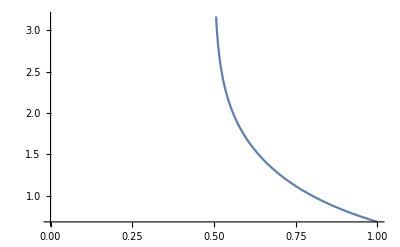

```mathematica
(*by plotting the others we can see that this is the only real solution:*)

sol[n_]:=ArcCosh[(√((2 n (1+2 (-1+n) n) (1+NN)+√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)];



NN=0.1

Plot[sol2[n],{n,0,1}]
```

```mathematica
sol2[1]
```

```mathematica
0.687465520005182
NN=.
```

```mathematica
(*now find the value of the optimized QFI*)
```

```mathematica
n=.
NN=.
Copt0=(√((2 n (1+2 (-1+n) n) (1+NN)+√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)
(*can factor out n and (1+NN) to get*)
Copt=√((2 (1+2 (-1+n)n)+√2 √(1+2 (-1+n) n))/(2  n (-1+2 n) (1+NN)))
```

(√((2 n (1+2 (-1+n) n) (1+NN)+√2 √(n^2 (1+2 (-1+n) n) (1+NN)^2))/(n^2 (-1+2 n) (1+NN)^2)))/(√2)

(√((√2 √(1+2 (-1+n) n)+2 (1+2 (-1+n) n))/(n (-1+2 n) (1+NN))))/(√2)

```mathematica
(*use expression from earlier ans substitute in the optimal Cosh[r2]*)

FullSimplify[(4 n NN (1+NN) (-1+(-1+2 n) (-1+n (2+NN)) Copt^2+2 (1-n) n (1+(1+NN) Copt^4)))/((-1+(1+NN) Copt^2) (1+2 (1-n) n (-1+(1+NN) Copt^2)))]
```

4 n NN (1+n (3+4 n^2-2 √(2+4 (-1+n) n)+2 n (-3+√(2+4 (-1+n) n))) NN)

0.1

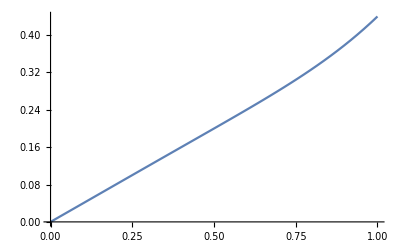

0.44

```mathematica
(*This simplifies to*)
MaxIQabovehalf[n_]:=4 *n* NN *(1+n*NN* (1-2*(1-n)*(2*n-1)-2*(1-n)*√(2+4 (-1+n) n)))
NN=0.1
Plot[MaxIQabovehalf[n],{n,0,1}]
MaxIQabovehalf[1]
NN=.
```

```mathematica
x=.
Factor[4*x^2-6*x+2]
```

2 (-1+x) (-1+2 x)